```mathematica
Table[{
With[{g= Graph[Table[With[{form=allGraphs6[k,"colofourrealnull"]},form-> Last[FactorTermsList[ DropMore[form,4,6]]]],{k,allGraphs6NullAtomKeys}],VertexLabels->"Name"]},
VertexInDegree[g,v]
],
v,
v/.repcolofourrealnullgraph2
},{v,realyNullAtomVars}]//Sort
```

{{5,n1234,-Graphics-n1234728},{10,n123x4,-Graphics-n123x4666},{10,n124x3,-Graphics-n124x3546},{10,n12x34,-Graphics-n12x34488},{10,n134x2,-Graphics-n134x2218},{10,n13x24,-Graphics-n13x24168},{10,n14x23,-Graphics-n14x2372},{10,n1x234,-Graphics-n1x23426},{17,n12x3x4,-Graphics-n12x3x4486},{17,n13x2x4,-Graphics-n13x2x4162},{17,n14x2x3,-Graphics-n14x2x354},{17,n1x23x4,-Graphics-n1x23x418},{17,n1x24x3,-Graphics-n1x24x36},{17,n1x2x34,-Graphics-n1x2x342},{26,n1x2x3x4,-Graphics-n1x2x3x40}}

```mathematica
Table[{
With[{g= Graph[Table[With[{form=allGraphs5[k,"colofourrealnull"]},form-> Last[FactorTermsList[ DropMore[form,4,5]]]],{k,allGraphs5NullAtomKeys}],VertexLabels->"Name"]},
VertexInDegree[g,v]
],
v,
v/.repcolofourrealnullgraph2
},{v,realyNullAtomVars}]//Sort
```

{{2,n1234,-Graphics-n1234728},{3,n123x4,-Graphics-n123x4666},{3,n124x3,-Graphics-n124x3546},{3,n12x34,-Graphics-n12x34488},{3,n134x2,-Graphics-n134x2218},{3,n13x24,-Graphics-n13x24168},{3,n14x23,-Graphics-n14x2372},{3,n1x234,-Graphics-n1x23426},{4,n12x3x4,-Graphics-n12x3x4486},{4,n13x2x4,-Graphics-n13x2x4162},{4,n14x2x3,-Graphics-n14x2x354},{4,n1x23x4,-Graphics-n1x23x418},{4,n1x24x3,-Graphics-n1x24x36},{4,n1x2x34,-Graphics-n1x2x342},{5,n1x2x3x4,-Graphics-n1x2x3x40}}

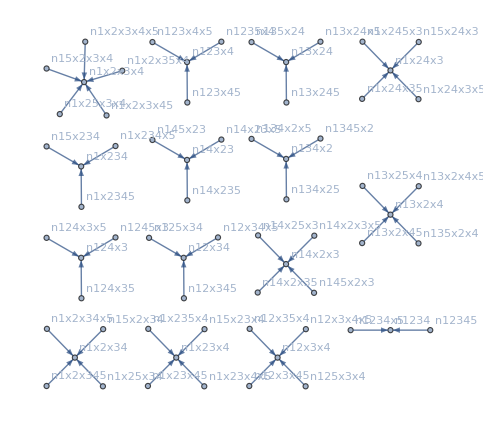

```mathematica
Graph[Table[With[{form=allGraphs5[k,"colofourrealnull"]},form-> Last[FactorTermsList[ DropMore[form,4,6]]]],{k,allGraphs5NullAtomKeys}],VertexLabels->"Name"]
```

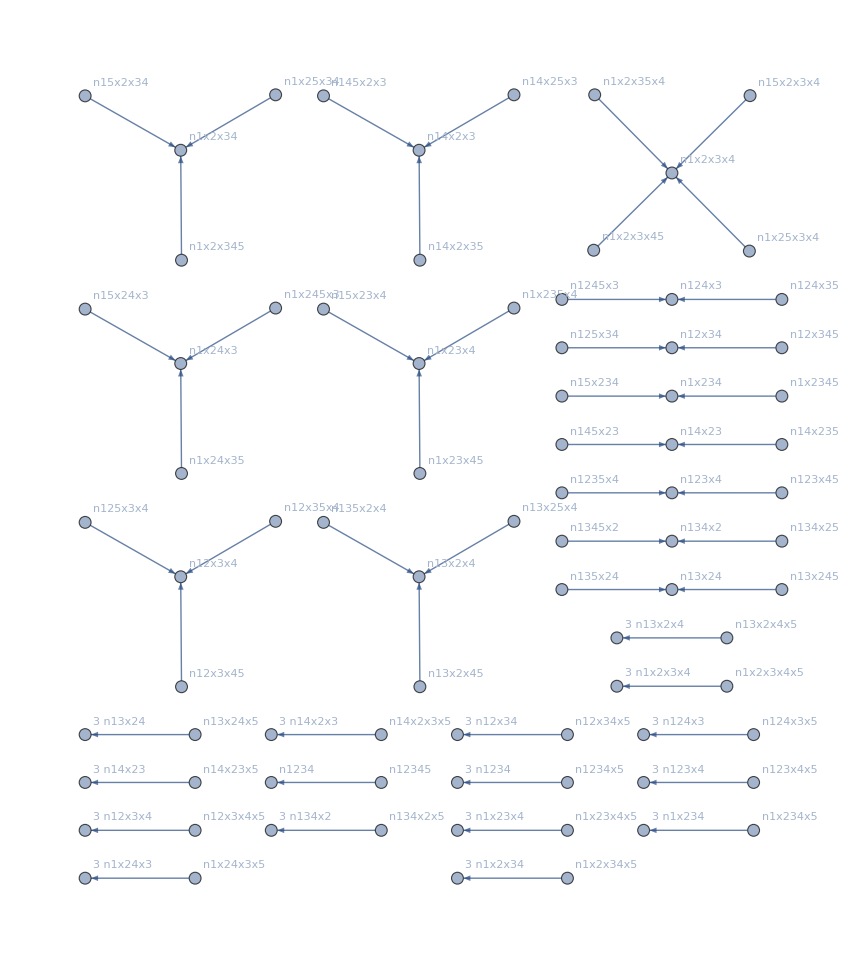

```mathematica
Block[
{result={},drop,prefix},
Table[With[{form=allGraphs5[k,"colofourrealnull"]},
drop=DropMore[form,4,5];
result=Append[result,form-> drop];

],{k,allGraphs5NullAtomKeys}]
;
Graph[result,VertexLabels->"Name"]
]
```